Wolfram Online Mini Campus. Part 12

Instagram Posts​
​Pinterest Posts​
​"Translation" of  SageMath Online Mini Campus. Part 12

Surfaces as Art Object

```mathematica
SphericalPlot3D[-Cos[3θ]-Cos[16θ]Sin[3ϕ],
{θ,0,2Pi},{ϕ,0,2Pi},PlotRange->All,
ImageSize->600,PlotPoints->25,Mesh->False,
Boxed->False,Axes->False,PlotStyle->Opacity[.8],
ColorFunction->Function[{x,y,z,θ,ϕ,r},
ColorData["BrightBands"][.45r]]]
```

-Graphics3D-

```mathematica
f=-.01Floor[3θ]-Exp[ϕ/4]; 
g=1.6(Sin[Floor[3θ]]+Cos[2θ]Sin[5ϕ]);
SphericalPlot3D[{f,g},{θ,0,2Pi},{ϕ,0,2Pi},
ImageSize->600,PlotRange->All,PlotPoints->17,
Mesh->False,Boxed->False,Axes->False,
PlotStyle->{Opacity[.3],Opacity[0.8]},
ExclusionsStyle->{None,Gray},
ColorFunction->Function[{x,y,z,θ,ϕ,r},
ColorData["BrightBands"][1-z]]]
```

-Graphics3D-

Graphs as Art Objects

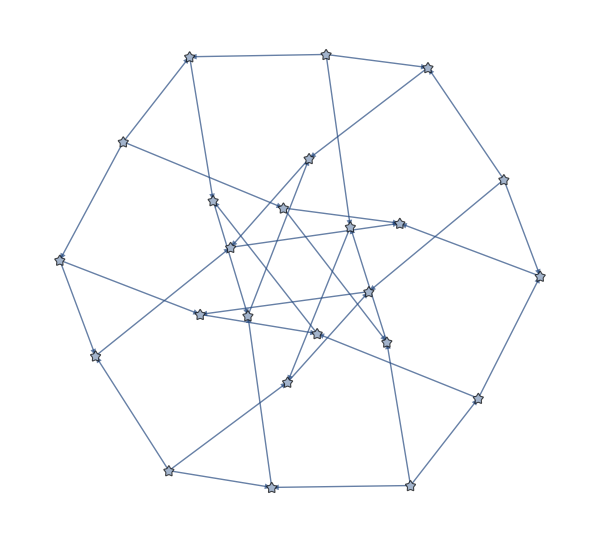

```mathematica
GS={"DodecahedralGraph","NauruGraph","IcosahedralGraph"};
CV[g_]:=Table[i->ColorData["BrightBands"]
[i/Length[GraphData[g,"Vertices"]]],
{i,GraphData[g,"Vertices"]}];
CE[g_]:=Flatten[Table[Table[i<->j->
ColorData["BrightBands"][i/Length[GraphData[g,"Vertices"]]],
{j,AdjacencyList[GraphData[g],i]}],{i,GraphData[g,"Vertices"]}]];
CGP=Function[{g,n},GraphPlot[GraphData[g,"Graph","All"][[n]],
VertexSize->.2,VertexStyle->CV[g],EdgeStyle->CE[g],
VertexShapeFunction->"ConcavePentagon",
EdgeShapeFunction->"CarvedArrow",ImageSize->600]];
CGP["NauruGraph",6]
```

```mathematica
PL="Edge Probability in Percentage"; 
RV=Table[t->ColorData["DeepSeaColors"][t/16],{t,16}];
VGP[p_]:=GraphPlot3D[RandomGraph[BernoulliGraphDistribution[16,
p/100]],ImageSize->Large,PlotLabel->{PL,ToString[p]},
GraphLayout ->"SpringElectricalEmbedding",
EdgeStyle->RGBColor["slategray"],VertexStyle->RV ];
VGP[90]
```

-Graphics3D-

Curves as Art Objects

```mathematica
ZV=Table[Table[{Re[Zeta[.1*(5+l*I)]],
Im[Zeta[(.1+.0005m)*(5+l*I)]]},
{l,Range[530]}],{m,Range[5]}];
Table[Graphics[Table[{Hue[l/530],
Line[{ZV[[K,l]],ZV[[K,l+1]]}]},{l,529}],
Axes->True,GridLines->Automatic,ImageSize->500,
GridLinesStyle->LightGray],{K,Range[4]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ContourPlot[(x^2-y)*Sin[x*y],{x,-3,3},{y,-3,3},
Contours->{-3,0,3},PlotPoints->10,ImageSize->Large,
ContourStyle->{Cyan,Directive[{White,Dashed}],Purple},
ColorFunction->"CandyColors",PlotLegends->Automatic,
ContourLabels->Function[{x,y,z},Style[Text[z,{x,y}],
{Cyan,White,Purple}[[z/3+2]],15]]]
```

-Graphics-

Linear Systems

```mathematica
P={{8,-5,-2,-2},{-2,4,-4,1},{-2,1,4,4},{4,1,3,10}}; 
Q={35,-8,-11,10};
Solve[P.{x1,x2,x3,x4}==Q,{x1,x2,x3,x4}]
{LinearSolve[P,Q],Inverse[P].Q}
{MapThread[Append,{P,Q}]//MatrixForm,
RowReduce[MapThread[Append,{P,Q}]][[All,5]]}
```

{{x1→1,x2→-5,x3→-3,x4→2}}

{{1,-5,-3,2},{1,-5,-3,2}}

{(8 | -5 | -2 | -2 | 35
-2 | 4 | -4 | 1 | -8
-2 | 1 | 4 | 4 | -11
4 | 1 | 3 | 10 | 10),{1,-5,-3,2}}

Matrix Operations

{{-134,195,-10,-99},{-106,-193,60,77}}

(-134 | 195 | -10 | -99
-106 | -193 | 60 | 77)

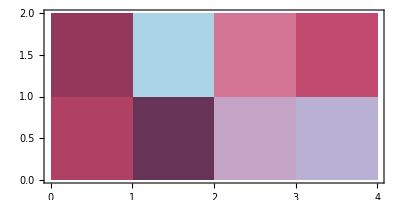

```mathematica
A2={{-3,-3,-6},{-4,-7,8}}; 
B2={{2,8,7},{-5,-6,-2},{-8,4,-8},{7,4,-6}};
C2={{-2,-4},{3,-5}}; 
D2={{-2,-3,-1,3},{-2,-9,8,9}};
alpha2=2; beta2 =-5;
M=alpha2*A2.Transpose[B2]+beta2*Transpose[C2].D2
MatrixForm[M]
MatrixPlot[M,ColorFunction->"CandyColors"]
```

HTML Exercises

```mathematica
EmbeddedHTML["<style>@import url('https://fonts.googleapis.com/css?family=Ewert');</style><script>function myFunction() {document.getElementById('demo').innerHTML=Date();}</script><button style='background-color:#3636ff; color:#fff; font-family:Ewert; font-size:150%;'onclick='myFunction();'>Click to Display Date and Time</button><p style='color:#3636ff; font-family:Ewert; font-size:120%;' id='demo'></p>",ImageSize->{900,120}]
```

Null<style>@import url('https://fonts.go…wert; font-size:120%;' id='demo'></p><style>@import url('https://fonts.googleapis.com/css?family=Ewert');</style><script>function myFunction() {document.getElementById('demo').innerHTML=Date();}</script><button style='background-color:#3636ff; color:#fff; font-family:Ewert; font-size:150%;'onclick='myFunction();'>Click to Display Date and Time</button><p style='color:#3636ff; font-family:Ewert; font-size:120%;' id='demo'></p>